# Entanglement Distillation: Quantum Circuit

See also Section 7.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Here, we start with a number of partially entangled pairs and “distills” a smaller number of maximally entangled pairs. This is illustrated in the quantum circuit model.

VonNeumannEntropy | VonNeumann entropy of a mixed state
PartialTrace | Partial trace over some subsystems
Dyad | Dyadic product of two vectors

Functions used in this document.

Make sure that Q3 is loaded.

```mathematica
<<Q3`
```

We have two parties Alice (A) and Bob (B). Teddy (T)  is an ancillary register to perform a measurement of the total Pauli Z.

```mathematica
Let[Qubit,A,B,T]
```

We will start with n partially entangled pairs.

```mathematica
$n=4;
kk=Range[$n];
AA=A[kk,None];
BB=B[kk,None];
```

You need fewer qubits for T, just enough to store the maximum number n.

```mathematica
ln=Ceiling@Log[2,$n+1];
TT=T[Range@ln,None];
```

## To Generate Partially Entangled Pairs

First construct a superposition with different amplitudes for the two computational basis states.

```mathematica
ϕ=2*Pi/3;
qc=QuantumCircuit[
LogicalForm[Ket[],A[1]],
Rotation[ϕ,A[1,2]]]
```

-Graphics-

```mathematica
Elaborate[qc]//ExpandAll//LogicalForm
```

(0_A_1)/2+1/2 √3 1_A_1

Then, by applying the CNOT gate, you can create a partially entangled pair.

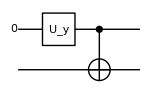

```mathematica
qc=QuantumCircuit[
LogicalForm[Ket[],A[1]],
Rotation[ϕ,A[1,2]],
CNOT[A[1],B[1]]]
```

```mathematica
out=Elaborate[qc];
LogicalForm[out]
```

1/2 0_A_10_B_1+1/2 √3 1_A_11_B_1

Examine the reduced density matrix for the first qubit to check that the above state is partial entangled.

```mathematica
rho=PartialTrace[out,B[1]];
Matrix[rho]//MatrixForm
```

(1/4 | 0
0 | 3/4)

Repeating the above procedure for other pairs, generate as many partially entangled pairs as  you like. In this particular example, we prepare four pairs.

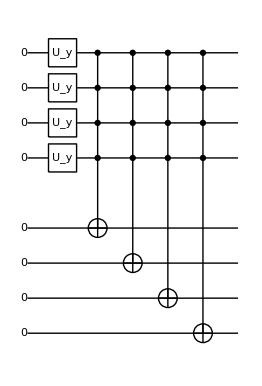

```mathematica
qc0=QuantumCircuit[
LogicalForm[Ket[],AA],
LogicalForm[Ket[],BB],
Rotation[ϕ,A[kk,2]],
Sequence@@Thread@CNOT[AA,BB],
"Invisible"->A[$n+1/2]
]
```

## Measurement of Total Pauli Z

We need to measure Z_tot:=Z_1+Z_2+…+Z_non Bob's (or, equivalently, Alice's) qubits.

```mathematica
bundle[]:=Flatten@Table[bundle[p],{p,$n}]
bundle[p_]:=With[
{logp=Ceiling@Log[2,p+1]},
Table[
CNOT[Prepend[T@Range[k-1],B[p]],T[k]],
{k,logp,1,-1}
]
]
```

The value of Z_tot is stored on Teddy's register.

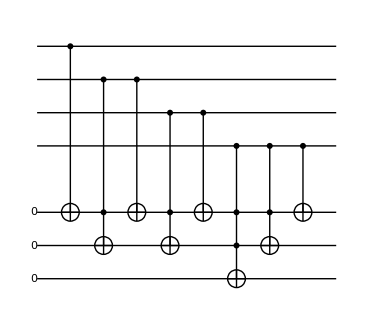

```mathematica
qc1=QuantumCircuit[
LogicalForm[Ket[],TT],
Sequence@@bundle[],
"Invisible"->B[$n+1/2]]
```

Let us check that the above quantum circuit indeed gives the sum of the bit values of the Bob’s qubits.

```mathematica
in=Basis[BB];
out=qc1**in;
```

```mathematica
sum=FromDigits[#,2]&/@Reverse/@Through[out[TT]];
Thread[SimpleForm[in]->sum]//TableForm
```

0000→0
0001→1
0010→1
0011→2
0100→1
0101→2
0110→2
0111→3
1000→1
1001→2
1010→2
1011→3
1100→2
1101→3
1110→3
1111→4

In actual situation, one must perform the measurement on Teddy's register in the computational basis. The measurement outcome refers to the value of Z_tot.

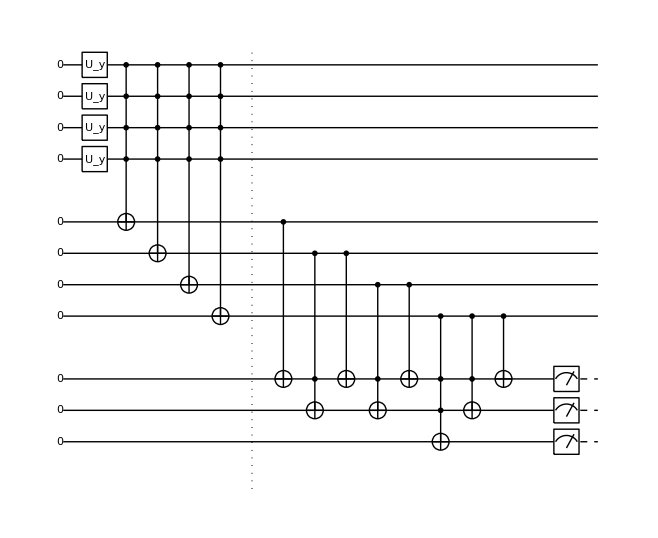

```mathematica
qc2=QuantumCircuit[
"Invisible"->{A[$n+1/2],B[$n+1/2],T[5]},
qc0,"Separator",qc1,"Spacer",Measurement[T[Range@ln,3]]]
```

## Transformation

The post-measurement state is spread over the four qubits of Alice's and Bob's registers, respectively. One has to transform it into a smaller number of pairs. Here, we assume that the measurement outcome is Z_tot=3, corresponding to two maximally entangled pairs. Note that  measurement outcome Z_tot=1also leads to two maximally entangled pairs since Binomial[4,1]==Binomial[4,3]==4.

To get the unitary transformation on Alice's side, we first rearrange the computational basis to get a new basis

𝒜:={0111,1011,1101,1110,α_5,…,α_16},

where α_k (k=5,…,16) are the computational basis states with total spin not equal to 3. Next, consider still another basis
	𝒜':={00;00,01;00,10;00,11;00,α'_5,…,α'_16},

where we have put a semicolon ';' to indicate the first two qubits to which encode Alice’s part of the maximally entangled states. Then, the required unitary transformation corresponds to the basis change from 𝒜 to 𝒜'. That is to say, the unitary transformation is given by

U:=00;000111+01;001011+10;001101+11;001110+Σ_(k=5)^16 a'_kα_k.

The unitary transformation on Bob's register may be obtained in the same manner, where we denote the rearranged bases by ℬ and ℬ'

### Method 1: Using Dyad

These are the computational bases for Alice's and Bob's registers, respectively.

```mathematica
bsA=Basis[AA]
bsB=Basis[BB]
```

{␣,1_A_4,1_A_3,1_A_31_A_4,1_A_2,1_A_21_A_4,1_A_21_A_3,1_A_21_A_31_A_4,1_A_1,1_A_11_A_4,1_A_11_A_3,1_A_11_A_31_A_4,1_A_11_A_2,1_A_11_A_21_A_4,1_A_11_A_21_A_3,1_A_11_A_21_A_31_A_4}

{␣,1_B_4,1_B_3,1_B_31_B_4,1_B_2,1_B_21_B_4,1_B_21_B_3,1_B_21_B_31_B_4,1_B_1,1_B_11_B_4,1_B_11_B_3,1_B_11_B_31_B_4,1_B_11_B_2,1_B_11_B_21_B_4,1_B_11_B_21_B_3,1_B_11_B_21_B_31_B_4}

These are the bases 𝒜 and ℬ for Alice's and Bob's registers, respectively.

```mathematica
bb=Permutations[PadLeft[Table[1,3],$n]];
sppA=Ket[AA->#]&/@bb;
sppB=Ket[BB->#]&/@bb;
sppA=Join[sppA,SortBy[Complement[bsA,sppA],LogicalForm[#,AA]&]];
sppB=Join[sppB,SortBy[Complement[bsB,sppB],LogicalForm[#,BB]&]];
```

```mathematica
sppA//LogicalForm
sppB//LogicalForm
```

{0_A_11_A_21_A_31_A_4,1_A_10_A_21_A_31_A_4,1_A_11_A_20_A_31_A_4,1_A_11_A_21_A_30_A_4,0_A_10_A_20_A_30_A_4,0_A_10_A_20_A_31_A_4,0_A_10_A_21_A_30_A_4,0_A_10_A_21_A_31_A_4,0_A_11_A_20_A_30_A_4,0_A_11_A_20_A_31_A_4,0_A_11_A_21_A_30_A_4,1_A_10_A_20_A_30_A_4,1_A_10_A_20_A_31_A_4,1_A_10_A_21_A_30_A_4,1_A_11_A_20_A_30_A_4,1_A_11_A_21_A_31_A_4}

{0_B_11_B_21_B_31_B_4,1_B_10_B_21_B_31_B_4,1_B_11_B_20_B_31_B_4,1_B_11_B_21_B_30_B_4,0_B_10_B_20_B_30_B_4,0_B_10_B_20_B_31_B_4,0_B_10_B_21_B_30_B_4,0_B_10_B_21_B_31_B_4,0_B_11_B_20_B_30_B_4,0_B_11_B_20_B_31_B_4,0_B_11_B_21_B_30_B_4,1_B_10_B_20_B_30_B_4,1_B_10_B_20_B_31_B_4,1_B_10_B_21_B_30_B_4,1_B_11_B_20_B_30_B_4,1_B_11_B_21_B_31_B_4}

These are the bases 𝒜' and ℬ' for Alice's and Bob's registers, respectively.

```mathematica
newA=Basis[A@{1,2}];
newB=Basis[B@{1,2}];
newA=Join[newA,SortBy[Complement[bsA,newA],LogicalForm[#,AA]&]];
newB=Join[newB,SortBy[Complement[bsB,newB],LogicalForm[#,BB]&]];
```

```mathematica
LogicalForm[newA]
LogicalForm[newB]
```

{0_A_10_A_20_A_30_A_4,0_A_11_A_20_A_30_A_4,1_A_10_A_20_A_30_A_4,1_A_11_A_20_A_30_A_4,0_A_10_A_20_A_31_A_4,0_A_10_A_21_A_30_A_4,0_A_10_A_21_A_31_A_4,0_A_11_A_20_A_31_A_4,0_A_11_A_21_A_30_A_4,0_A_11_A_21_A_31_A_4,1_A_10_A_20_A_31_A_4,1_A_10_A_21_A_30_A_4,1_A_10_A_21_A_31_A_4,1_A_11_A_20_A_31_A_4,1_A_11_A_21_A_30_A_4,1_A_11_A_21_A_31_A_4}

{0_B_10_B_20_B_30_B_4,0_B_11_B_20_B_30_B_4,1_B_10_B_20_B_30_B_4,1_B_11_B_20_B_30_B_4,0_B_10_B_20_B_31_B_4,0_B_10_B_21_B_30_B_4,0_B_10_B_21_B_31_B_4,0_B_11_B_20_B_31_B_4,0_B_11_B_21_B_30_B_4,0_B_11_B_21_B_31_B_4,1_B_10_B_20_B_31_B_4,1_B_10_B_21_B_30_B_4,1_B_10_B_21_B_31_B_4,1_B_11_B_20_B_31_B_4,1_B_11_B_21_B_30_B_4,1_B_11_B_21_B_31_B_4}

Finally, the unitary transformation is constructed as prescribed above.

```mathematica
trsA=Total@MapThread[Dyad[#1,#2,AA]&,{newA,sppA}]
trsB=Total@MapThread[Dyad[#1,#2,BB]&,{newB,sppB}]
```

0_A_10_A_20_A_30_A_40_A_11_A_21_A_31_A_4+1_A_10_A_20_A_30_A_41_A_11_A_20_A_31_A_4+1_A_11_A_20_A_30_A_41_A_11_A_21_A_30_A_4+1_A_11_A_21_A_30_A_41_A_11_A_20_A_30_A_4+1_A_11_A_21_A_31_A_41_A_11_A_21_A_31_A_4+1_A_11_A_20_A_31_A_41_A_10_A_21_A_30_A_4+1_A_10_A_21_A_30_A_41_A_10_A_20_A_30_A_4+1_A_10_A_21_A_31_A_41_A_10_A_20_A_31_A_4+1_A_10_A_20_A_31_A_40_A_11_A_21_A_30_A_4+0_A_11_A_20_A_30_A_41_A_10_A_21_A_31_A_4+0_A_11_A_21_A_30_A_40_A_11_A_20_A_30_A_4+0_A_11_A_21_A_31_A_40_A_11_A_20_A_31_A_4+0_A_11_A_20_A_31_A_40_A_10_A_21_A_31_A_4+0_A_10_A_21_A_30_A_40_A_10_A_20_A_31_A_4+0_A_10_A_21_A_31_A_40_A_10_A_21_A_30_A_4+0_A_10_A_20_A_31_A_40_A_10_A_20_A_30_A_4

0_B_10_B_20_B_30_B_40_B_11_B_21_B_31_B_4+1_B_10_B_20_B_30_B_41_B_11_B_20_B_31_B_4+1_B_11_B_20_B_30_B_41_B_11_B_21_B_30_B_4+1_B_11_B_21_B_30_B_41_B_11_B_20_B_30_B_4+1_B_11_B_21_B_31_B_41_B_11_B_21_B_31_B_4+1_B_11_B_20_B_31_B_41_B_10_B_21_B_30_B_4+1_B_10_B_21_B_30_B_41_B_10_B_20_B_30_B_4+1_B_10_B_21_B_31_B_41_B_10_B_20_B_31_B_4+1_B_10_B_20_B_31_B_40_B_11_B_21_B_30_B_4+0_B_11_B_20_B_30_B_41_B_10_B_21_B_31_B_4+0_B_11_B_21_B_30_B_40_B_11_B_20_B_30_B_4+0_B_11_B_21_B_31_B_40_B_11_B_20_B_31_B_4+0_B_11_B_20_B_31_B_40_B_10_B_21_B_31_B_4+0_B_10_B_21_B_30_B_40_B_10_B_20_B_31_B_4+0_B_10_B_21_B_31_B_40_B_10_B_21_B_30_B_4+0_B_10_B_20_B_31_B_40_B_10_B_20_B_30_B_4

By construction, the unitary transformations are just permutation, which is clear from their matrix representations.

```mathematica
Matrix[trsA]//MatrixForm
Matrix[trsB]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Check that they are indeed unitary transformations.

```mathematica
Dagger[trsA]**trsA//Elaborate
Dagger[trsB]**trsB//Elaborate
```

1

1

### Method 2: Using Permutation

Here, we find the permutation corresponding to the basis change and use it to construct the unitary matrix.

```mathematica
constructUnitary::bad="States with `` non-zero qubits in total `` qubits cannot be encoded in a finite number of qubits.";
constructUnitary[m_Integer,n_Integer]:=Module[
{org=Tuples[{0,1},n],
bin=Log[2,Binomial[n,m]],
src,dst},
If[Not@IntegerQ@bin,
Message[constructUnitary::bad,m,n];
Return[One@Power[2,n]]
];
src=Permutations@PadLeft[Table[1,m],n];
src=DeleteDuplicates@Join[src,org];
dst=PadRight[#,n]&/@Tuples[{0,1},bin];
dst=DeleteDuplicates@Join[dst,org];
tau=FindPermutation[src,org];
tau=FindPermutation@Permute[dst,tau];
PermutationMatrix[tau,Power[2,n]]
]
```

```mathematica
mat=constructUnitary[3,4];
mat//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
trsA=ExpressionFor[mat,AA]//Elaborate;
trsB=ExpressionFor[mat,BB]//Elaborate;
```

```mathematica
Dagger[trsA]**trsA
Dagger[trsB]**trsB
```

1

1

## Overall

Now, we have all components. Our desired quantum circuit is as follows. The first part generates four partially entangled pairs, the second measures the total Pauli Z on Bob's register, and the last transforms the post-measurement state a fixed pair of qubits from Alice's and Bob's registers.

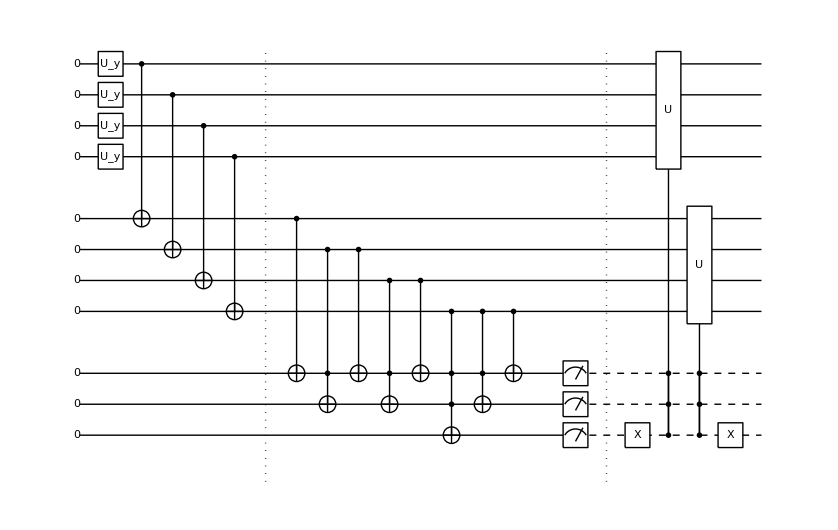

```mathematica
all=QuantumCircuit[qc2,"Separator",
T[3,1],
ControlledU[T@{1,2,3},trsA,"Label"->"U"],
ControlledU[T@{1,2,3},trsB,"Label"->"U"],
T[3,1]]
```

Because the transformation on Alice’s and Bob’s sides are designed for the measurement outcome of Z_tot=3, we just run the quantum circuit until we get the desired outcome.

```mathematica
Until[ztot==3,
out=Elaborate[all];
ztot=FromDigits[Reverse@Readout[Through[TT[3]]],2];
PrintTemporary["Z_tot=",ztot]
];
```

Here is the output state of the total system. Obviously, the whole register T is separated from the other two registers. So are the last two registers of the respective registers A and B.

```mathematica
LogicalForm[out,Join[AA,BB,TT]]
```

1/2 0_A_10_A_20_A_30_A_40_B_10_B_20_B_30_B_41_T_11_T_20_T_3+1/2 0_A_11_A_20_A_30_A_40_B_11_B_20_B_30_B_41_T_11_T_20_T_3+1/2 1_A_10_A_20_A_30_A_41_B_10_B_20_B_30_B_41_T_11_T_20_T_3+1/2 1_A_11_A_20_A_30_A_41_B_11_B_20_B_30_B_41_T_11_T_20_T_3

Focusing on the two first two qubits of registers A and B, we see that there are two maximally entangled pairs.

```mathematica
SimpleForm[out,{A@{1,2},B@{1,2}}]
```

(00;00)/2+(01;01)/2+(10;10)/2+(11;11)/2

```mathematica
KetFactor@KetDrop[out,TT]
```

1/2 (0_A_10_B_1+1_A_11_B_1)⊗(0_A_20_B_2+1_A_21_B_2)

Related Guides

Quantum Computation and Information

Related Tech Notes

Entanglement Distillation

Quantum Information Theory

Quantum Computation and Information: Overview

Related Links

J. Preskill (1998), Lecture Notes for Physics 229: Quantum Information and Computation.

M. Nielsen and I. L. Chuang (2022), Quantum Computation and Quantum Information (Cambridge University Press, 2011).

Mahn-Soo Choi (2022), A Quantum Computation Workbook (Springer, 2022).

## Metadata

### Categorization

Tech Note

QuantumWorkbook

QuantumWorkbook`

QuantumWorkbook/tutorial/EntanglementDistillationQuantumCircuit

### Keywords

quantum entanglement

entanglement distillation

entanglement purification